```mathematica
(*1s=2.9979*10^8m, 1kg=7.4262*10^-28m, 1J=8.2627*10^-45m, 1eV=1.3239*10^-63m)
```

```mathematica
μe=2;
me=6.7648*10^-58;
mH=1.2428*10^-54;
c=1;
h=1.6414*10^-69;
Msun=1476.7;
r0=10^6;
b=0.01*r0;
ρc0=10^13*7.4262*10^-28;
σ0=10^20;
```

```mathematica
(*本文的条件*)
p[ρ[x_]]:=(Pi*me^4*c^5)/(3*h^3)*((((3*h^3*ρ[x])/(8*Pi*μe*mH*(me*c)^3))^(1/3))*(2*(((3*h^3*ρ[x])/(8*Pi*μe*mH*(me*c)^3))^(1/3))^2-3)*Sqrt[(((3*h^3*ρ[x])/(8*Pi*μe*mH*(me*c)^3))^(1/3))^2+1]+3*ArcSinh[((3*h^3*ρ[x])/(8*Pi*μe*mH*(me*c)^3))^(1/3)]);
ρe[x_]:=σ0/(Pi^(3/2)*b*(2*(radius*r0)^2+b^2))*Exp[-(x*r0-r0*radius)^2/b^2];
(*radius=10*)
```

```mathematica
(*QS*)
α=0.4;
B=60*(1.6022*10^-19*10^6)/10^-45*8.24*10^-45;
p[ρ[x_]]:=(ρ[x]-4*B)/3;
ρe[x_]:=α*ρ[x];
```

```mathematica
sol=NDSolve[{D[q[x],x]/r0==4*Pi*ρe[x]*(x*r0)^2*(1-(2*Msun*y[x])/(r0*x)+q[x]^2/(r0*x)^2)^(-1/2),(Msun*D[y[x],x])/r0==4*Pi*(x*r0)^2*ρ[x]+q[x]/(r0*x)*D[q[x],x]/r0,D[p[ρ[x]],x]/r0==-(p[ρ[x]]+ρ[x])*(4*Pi*(r0*x)*p[ρ[x]]+(Msun*y[x])/(r0*x)^2-q[x]^2/(r0*x)^3)*(1-(2*Msun*y[x])/(r0*x)+q[x]^2/(r0*x)^2)^(-1)+q[x]/(4*Pi*(r0*x)^4)*D[q[x],x]/r0,q[10^-5]==10^-10,y[10^-5]==10^-10,ρ[10^-5]==ρc0(*,p[ρ[radius]]==10^-10*)}/.radius->10,{q,y,ρ},{x,10^-5,10}]
```

{{q→InterpolatingFunction[…],y→InterpolatingFunction[…],ρ→InterpolatingFunction[…]}}

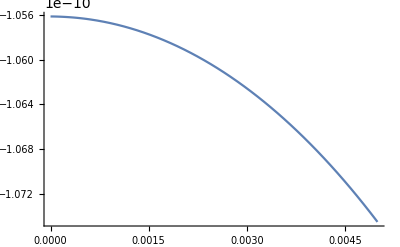

-Graphics-

```mathematica
Plot[p[ρ[x]]/.sol,{x,10^-15,.005},PlotRange->All]
Plot[ρ[x]/ρc0/.sol,{x,10^-15,10.},PlotRange->All]
```

尝试不使用[km]

```mathematica
p[r_]:=(Pi*me^4*c^5)/(3*h^3)*((((3*h^3*ρ[r])/(8*Pi*μe*mH*(me*c)^3))^(1/3))*(2*(((3*h^3*ρ[r])/(8*Pi*μe*mH*(me*c)^3))^(1/3))^2-3)*Sqrt[(((3*h^3*ρ[r])/(8*Pi*μe*mH*(me*c)^3))^(1/3))^2+1]+3*ArcSinh[((3*h^3*ρ[r])/(8*Pi*μe*mH*(me*c)^3))^(1/3)]);
ρe[r_]:=σ0/(Pi^(3/2)*b*(2*(10^4)^2+b^2))*Exp[-(r-10^4)^2/b^2];
(*radius=10^4*)
```

```mathematica
sol=NDSolve[{D[q[r],r]==4*Pi*ρe[r]*r^2*(1-(2*m[r])/r+q[r]^2/r^2)^(-1/2),D[m[r],r]==4*Pi*r^2*ρ[r]+(q[r]*D[q[r],r])/r,D[p[r],r]==-(p[r]+ρ[r])*(4*Pi*r*p[r]+m[r]/r^2*q[r]^2/r^3)*(1-(2*m[r])/r+q[r]^2/r^2)^(-1)+q[r]/(4*Pi*r^4)*D[q[r],r],q[10^-15]==0,m[10^-15]==0,ρ[10^-15]==ρc0},{q,m,ρ},{r,10^-15,100}]
```

NDSolve::ndsz: 在 r == 0.000456561 处，步长实际上为零；可能存在奇点或者刚性系统.

{{q→InterpolatingFunction[…],m→InterpolatingFunction[…],ρ→InterpolatingFunction[…]}}

```mathematica
Plot[p[ρ[x]]/.sol,{x,10^-15,10.},PlotRange->All]
Plot[ρ[x]/ρc0/.sol,{x,10^-15,10.},PlotRange->All]
```

```mathematica
Quit[]
```